```mathematica
NotebookEvaluate["/Users/claireplunkett/Documents/REU/MAR_dataruns0Claire.nb"]; (* Evaluate the main data and functions *)
```

MAR_functions evaluation complete!

Inverse::luc: Result for Inverse of badly conditioned matrix «1» may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{25.,125.266,79.9162,79.7768,67.4355,107.138,21.1817,-65.0677},«6»,{-65.0677,-326.031,«4»,-27.886,263.632}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

## Testing Data Generation

```mathematica
(* This function generates a B matrix based on the statistics of three potential types of B matrices (composite, individual, and averaged), generates data from that B matrix based on multiple Sigma matrices, and then plots the mean, standard deviation, and CVs of the data set for each type of B matrix *)
(* This is not very useful *)
```

```mathematica
analyzeData[size_,tanks_,time_,numberBs_,numberSigs_]:=Module[{currentSigma,currentBAveraged,currentBComposite,currentBIndividual,currentDataAveraged,currentDataComposite,currentDataIndividual,species,CV,h},
For[i=1,i≤size,i++,
species[i]={{0,0},{0,0},{0,0}};
CV[i]={0,0,0};
];
For[h=1,h≤numberSigs,h++,
currentSigma=GenSigma[size];

For[j=1,j≤numberBs,j++,
currentBComposite=GenBComposite[size];
currentBIndividual=GenBIndividual[size];
currentBAveraged=GenBAveraged[size];
currentDataComposite=GenData[currentBComposite,currentSigma,tanks,time];
currentDataIndividual=GenData[currentBIndividual,currentSigma,tanks,time];
currentDataAveraged=GenData[currentBAveraged,currentSigma,tanks,time];

For[i=1,i≤size,i++,
species[i]=species[i]+{{Mean[Mean[Exp[Transpose[currentDataComposite[[All,All,i]]]]]],Mean[StandardDeviation[Exp[Transpose[currentDataComposite[[All,All,i]]]]]]},{Mean[Mean[Exp[Transpose[currentDataAveraged[[All,All,i]]]]]],Mean[StandardDeviation[Exp[Transpose[currentDataAveraged[[All,All,i]]]]]]},{Mean[Mean[Exp[Transpose[currentDataIndividual[[All,All,i]]]]]],Mean[StandardDeviation[Exp[Transpose[currentDataIndividual[[All,All,i]]]]]]}};
CV[i]=CV[i]+{Mean[Mean[Exp[Transpose[currentDataComposite[[All,All,i]]]]]]/Mean[StandardDeviation[Exp[Transpose[currentDataComposite[[All,All,i]]]]]],Mean[Mean[Exp[Transpose[currentDataAveraged[[All,All,i]]]]]]/Mean[StandardDeviation[Exp[Transpose[currentDataAveraged[[All,All,i]]]]]],Mean[Mean[Exp[Transpose[currentDataIndividual[[All,All,i]]]]]]/Mean[StandardDeviation[Exp[Transpose[currentDataIndividual[[All,All,i]]]]]]};
];
];
];
For[i=1,i≤size,i++,
species[i]=species[i]/numberBs/numberSigs;
CV[i]=CV[i]/numberBs/numberSigs;
];
GraphicsRow[{BarChart[Log[Partition[Flatten[species[#]&/@Range[1,size]],6]],PlotLabel->"Mean and Standard Deviation for Each Species",ChartLegends->{"Composite Mean","Composite SD","Averaged Mean","Averaged SD","Individual Mean","Individual SD"},ImageSize->Medium],BarChart[Partition[Flatten[CV[#]&/@Range[4]],3],PlotLabel->"CV for Each Species"]}]
]
```

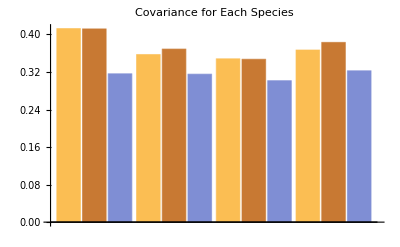

```mathematica
analyzeData[4,10,25,10,10](*species, tanks, time, numberBs, numberSigs*)
```

## Histograms comparing Matrix Statistics

### Functions

```mathematica
(* A function that makes composing a list for a histogram easy *)
HistList[list_,function_,matrix_]:=Module[{},
Join[list,{function[matrix]}]
]
```

```mathematica
(* Here is a collection of functions that give a numerical property of a matrix: *)
MaxEig[matrix_]:=Max[Abs[Eigenvalues[matrix]]]
IntrinsicStochasticInvariability[bmatrix_]:=1/Norm[Inverse[IdentityMatrix[Dimensions[bmatrix][[1]]^2]-KroneckerProduct[bmatrix,bmatrix]],2]
MeanInteractionStrength[bmatrix_]:=Total[Abs[bmatrix],2]/Dimensions[bmatrix][[1]]/Dimensions[bmatrix][[2]]
MeanInteractionStrengthExact[bmatrix_]:=Total[bmatrix,2]/Dimensions[bmatrix][[1]]/Dimensions[bmatrix][[2]]
MeanOffDiagonalInteractionStrength[bmatrix_]:=Total[Abs[UpperTriangularize[bmatrix,1]+LowerTriangularize[bmatrix,-1]],2]/(Dimensions[bmatrix][[1]]^2-Dimensions[bmatrix][[1]])
Reactivity[matrix_]:=Max[Eigenvalues[Transpose[matrix].matrix]]
FrobeniusNorm[matrix_]:=Norm[matrix,"Frobenius"]
```

```mathematica
(* This function creates a histogram of a property (function) of B matrices based on generated data WITHOUT covariates
This uses composite, individual, and averaged matrices 
Specify the function, the number of species, and if you want to use GenData or GenDataConsistent (see functions.nb for more information) *)
ThreeHists[function_,size_,generator_]:=Module[{listC,listA,listI,useB,useSigma,useData,newBC,newBA,newBI},
listC={};
listA={};
listI={};
useB=GenBAveraged[size];
For[i=1,i≤500,i++,
useSigma=GenSigma[size];
useData=generator[useB,useSigma,10,25]; (* the first number is the number of tanks, the second number is the length of time *)
newBC=B[MAR[useData,0,{}]];
newBA=Table[0,{i,1,size},{j,1,size}];
For[j=1,j≤10,j++,
newBI=B[MAR[{useData[[j]]},0,{}]];
newBA=newBI+newBA;
listI=HistList[listI,function,newBI];
];
newBA=newBA/10;
listC=HistList[listC,function,newBC];
listA=HistList[listA,function,newBA];
];
GraphicsRow[{Show[SmoothHistogram[listA,Epilog->Line[{{function[useB],0},{function[useB],150}}],PlotStyle->Blue,PlotRange->All],SmoothHistogram[listC,PlotStyle->Orange,PlotRange->All],SmoothHistogram[listI,PlotStyle->Purple,PlotRange->All],PlotLabel->function,PlotRange->All],LineLegend[{Blue,Orange,Purple},{"Averaged","Composite","Individual"}]},ImageSize->{700,300}]
]
```

```mathematica
(* This function creates a histogram of a property (function) of B matrices based on generated data WITH covariates
This uses composite, individual, and averaged matrices 
Specify the function, the number of species, the number of covariates, and if you want to use GenDataWithC or GenDataWithCNoisy (see functions.nb for more information) *)
ThreeHistsWithC[function_,size_,covsize_,generator_]:=Module[{listC,listA,listI,useB,useC,useSigma,useData,newBC,newBA,newBI},
listC={};
listA={};
listI={};
useB=GenBAveraged[size];
useC=GenC[size,covsize];
For[i=1,i≤500,i++,
useSigma=GenSigma[size];
useData=generator[useB,useC,useSigma,10,25,10];  (* the first number is the number of tanks, the second number is the length of time, the third is "fudge time" to let the system settle to an equilibrium *)
newBC=B[MAR[useData,covsize,{}]];
newBA=Table[0,{i,1,size},{j,1,size}];
For[j=1,j≤10,j++,
newBI=B[MAR[{useData[[j]]},covsize,{}]];
newBA=newBI+newBA;
listI=HistList[listI,function,newBI];
];
newBA=newBA/10;
listC=HistList[listC,function,newBC];
listA=HistList[listA,function,newBA];
];
GraphicsRow[{Show[SmoothHistogram[listA,Epilog->Line[{{function[useB],0},{function[useB],150}}],PlotStyle->Blue,PlotRange->All],SmoothHistogram[listC,PlotStyle->Orange,PlotRange->All],SmoothHistogram[listI,PlotStyle->Purple,PlotRange->All],PlotLabel->function,PlotRange->All],LineLegend[{Blue,Orange,Purple},{"Averaged","Composite","Individual"}]},ImageSize->{700,300}]
]
```

```mathematica
(* This function creates a histogram of a property (function) of B matrices and C matrices based on generated data WITH covariates
This uses composite, individual, and averaged matrices 
Specify the function, the number of species, and the number of covariates
This function uses GenDataWithC (see functions.nb for more information) *)
SixHists[function_,size_,covsize_]:=Module[{listC,listA,listI,listCc,listAc,listIc,useB,useC,useSigma,useData,newMC,newMA,newMI,newBC,newBA,newBI,newCC,newCA,newCI},
listC={};
listA={};
listI={};
listCc={};
listAc={};
listIc={};
useB=GenBAveraged[size];
useC=GenC[size,covsize];
For[i=1,i≤500,i++,
useSigma=GenSigma[size];
useData=GenDataWithC[useB,useC,useSigma,10,25,10];
newMC=MAR[useData,covsize,{}];
newBC=B[newMC];
newCC=Cmat[newMC,covsize];
newMA=Table[0,{i,1,size},{j,1,size+covsize+1}];
newBA=Table[0,{i,1,size},{j,1,size}];
newCA=Table[0,{i,1,size},{j,1,covsize}];
For[j=1,j≤10,j++,
newMI=MAR[{useData[[j]]},covsize,{}];
newBI=B[newMI];
newCI=Cmat[newMI,covsize];
newBA=newBI+newBA;
newCA=newCI+newCA;
listI=HistList[listI,function,newBI];
listIc=HistList[listIc,function,newCI];
];
newBA=newBA/10;
newCA=newCA/10;
listC=HistList[listC,function,newBC];
listA=HistList[listA,function,newBA];
listCc=HistList[listCc,function,newCC];
listAc=HistList[listAc,function,newCA];
];
GraphicsRow[{Show[SmoothHistogram[listA,Epilog->Line[{{function[useB],0},{function[useB],150}}],PlotStyle->Blue,PlotRange->All],SmoothHistogram[listC,PlotStyle->Orange,PlotRange->All],SmoothHistogram[listI,PlotStyle->Purple,PlotRange->All],PlotLabel->ToString[function]<>" B",PlotRange->All],LineLegend[{Blue,Orange,Purple},{"Averaged","Composite","Individual"}],Show[SmoothHistogram[listAc,Epilog->Line[{{function[useC],0},{function[useC],150}}],PlotStyle->Blue,PlotRange->All],SmoothHistogram[listCc,PlotStyle->Orange,PlotRange->All],SmoothHistogram[listIc,PlotStyle->Purple,PlotRange->All],PlotLabel->ToString[function]<>" C",PlotRange->All]},ImageSize->{1000,300}]
]
```

```mathematica
(* This function creates a histogram of a property (function) of the difference between generated C matrices and the original C matrix based on generated data
This uses composite, individual, and averaged matrices 
Specify the function, the number of species, and the number of covariates
This function uses GenDataWithC (see functions.nb for more information) *)
CHistsDifference[function_,size_,covsize_]:=Module[{listCc,listAc,listIc,useB,useC,useSigma,useData,newMC,newMA,newMI,newBC,newBA,newBI,newCC,newCA,newCI},
listCc={};
listAc={};
listIc={};
useB=GenBAveraged[size];
useC=GenC[size,covsize];
For[i=1,i≤500,i++,
useSigma=GenSigma[size];
useData=GenDataWithC[useB,useC,useSigma,10,25,10];
newMC=MAR[useData,covsize,{}];
newCC=Cmat[newMC,covsize]-useC;
newMA=Table[0,{i,1,size},{j,1,size+covsize+1}];
newCA=Table[0,{i,1,size},{j,1,covsize}];
For[j=1,j≤10,j++,
newMI=MAR[{useData[[j]]},covsize,{}];
newCI=Cmat[newMI,covsize]-useC;
newCA=newCI+newCA;
listIc=HistList[listIc,function,newCI];
];
newCA=newCA/10;
listCc=HistList[listCc,function,newCC];
listAc=HistList[listAc,function,newCA];
];
GraphicsRow[{Show[SmoothHistogram[listAc,PlotStyle->Blue],SmoothHistogram[listCc,PlotStyle->Orange],SmoothHistogram[listIc,PlotStyle->Purple],PlotLabel->function,PlotRange->{0,All}],LineLegend[{Blue,Orange,Purple},{"Averaged","Composite","Individual"}]},ImageSize->{700,300}]
]
```

```mathematica
(* This function creates a histogram of a property (function) of A vectors based on generated data with covariates
This uses composite, individual, and averaged matrices 
Specify the function, the number of species, and the number of covariates
This function uses GenDataWithC (see functions.nb for more information) *)
AHists[function_,size_,covsize_]:=Module[{listC,listA,listI,useB,useC,useSigma,useData,newMC,newMA,newMI,newAC,newAA,newAI},
listC={};
listA={};
listI={};
useB=GenBAveraged[size];
useC=GenC[size,covsize];
For[i=1,i≤500,i++,
useSigma=GenSigma[size];
useData=GenDataWithC[useB,useC,useSigma,10,100,10];
newMC=MAR[useData,covsize,{}];
newAC=newMC[[All,1]];
newMA=Table[0,{i,1,size},{j,1,size+covsize+1}];
newAA=Table[0,{i,1,size}];
For[j=1,j≤10,j++,
newMI=MAR[{useData[[j]]},covsize,{}];
newAI=newMI[[All,1]];
newAA=newAI+newAA;
listI=HistList[listI,function,newAI];
];
newAA=newAA/10;
listC=HistList[listC,function,newAC];
listA=HistList[listA,function,newAA];
];
GraphicsRow[{Show[SmoothHistogram[listA,PlotStyle->Blue],SmoothHistogram[listC,PlotStyle->Orange],SmoothHistogram[listI,PlotStyle->Purple],PlotLabel->function,PlotRange->{0,All}],LineLegend[{Blue,Orange,Purple},{"Averaged","Composite","Individual"}]},ImageSize->{700,300}]
]

ThreeHistsAllTime[function_,size_,covsize_,generator_]:=Module[{listC,listA,listCall,listAall,useB,useC,useSigma,useData,useDataAll,useDataEarly,newBC,newBA,newBI,newBCall,newBAall,newBIall,fudge},
listC={};
listA={};
listCall={};
listAall={};
useB=GenBAveraged[size];
useC=GenC[size,covsize];
For[i=1,i≤500,i++,
useSigma=GenSigma[size];
useDataAll=generator[useB,useC,useSigma,10,35,0]; (* Returns 35 *)
fudge =RandomInteger[{0,5}]; (* Randomly uses a fudge time of 0 to 5 for each set of data *)
useData=useDataAll[[All,11;;35]];(* fudge time of 10 ensures that the data is around the equilibrium *)
useDataEarly=useDataAll[[All,fudge+1;;26+fudge]];(* random fudge time but same number of data points *)
newBC=B[MAR[useData,covsize,{}]];
newBCall=B[MAR[useDataEarly,covsize,{}]];
newBA=Table[0,{i,1,size},{j,1,size}];
newBAall=Table[0,{i,1,size},{j,1,size}];
For[j=1,j≤10,j++,
newBI=B[MAR[{useData[[j]]},covsize,{}]];
newBIall=B[MAR[{useDataEarly[[j]]},covsize,{}]];
newBA=newBI+newBA;
newBAall=newBIall+newBAall;
];
newBA=newBA/10;
newBAall=newBAall/10;
listC=HistList[listC,function,newBC];
listA=HistList[listA,function,newBA];
listCall=HistList[listCall,function,newBCall];
listAall=HistList[listAall,function,newBAall];
];
GraphicsRow[{Show[SmoothHistogram[listA,Epilog->Line[{{function[useB],0},{function[useB],150}}],PlotStyle->Blue,PlotRange->All],SmoothHistogram[listC,PlotStyle->Orange,PlotRange->All],SmoothHistogram[listAall,PlotStyle->{Dashed,Blue},PlotRange->All],SmoothHistogram[listCall,PlotStyle->{Dashed,Orange},PlotRange->All],PlotRange->All,PlotLabel->function],LineLegend[{Blue,{Blue,Dashed},Orange,{Orange,Dashed}},{"Averaged","Averaged Full","Composite","Composite Full"}]},ImageSize->{700,300}]
]
```

### Histograms without Covariates

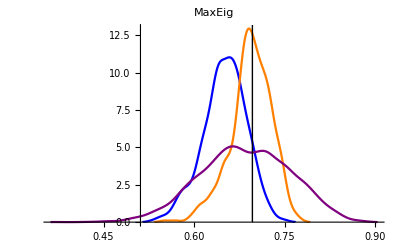

```mathematica
ThreeHists[MaxEig,4,GenData]
```

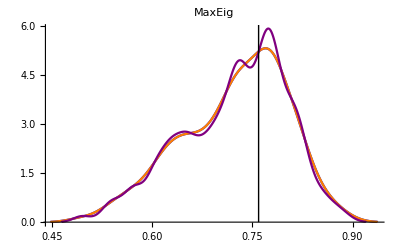

```mathematica
ThreeHists[MaxEig,4,GenDataConsistent]
```

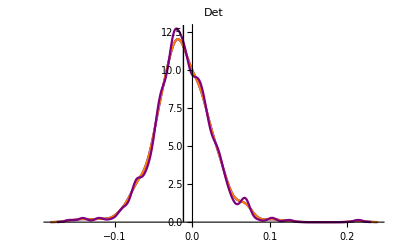

```mathematica
ThreeHists[Det,4,GenDataConsistent]
```

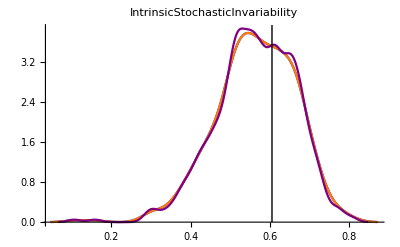

```mathematica
ThreeHists[IntrinsicStochasticInvariability,4,GenDataConsistent]
```

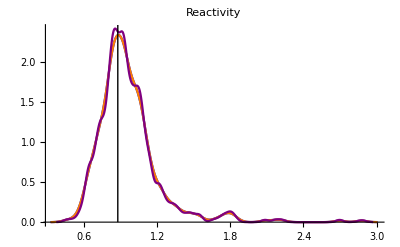

```mathematica
ThreeHists[Reactivity,4,GenDataConsistent]
```

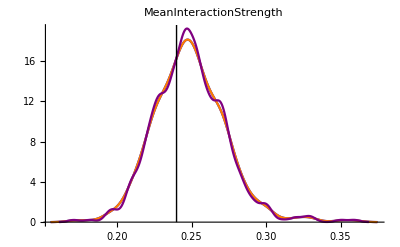

```mathematica
ThreeHists[MeanInteractionStrength,4,GenDataConsistent]
```

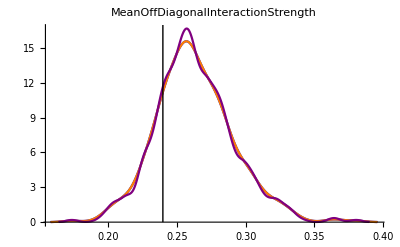

```mathematica
ThreeHists[MeanOffDiagonalInteractionStrength,4,GenDataConsistent]
```

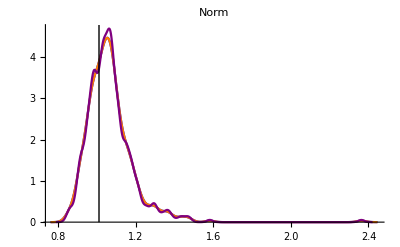

```mathematica
ThreeHists[Norm,4,GenDataConsistent]
```

### Histograms with Covariates

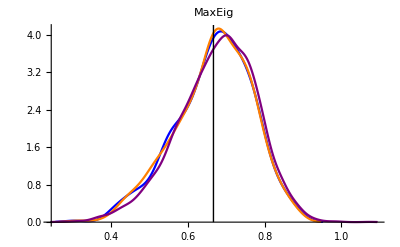

```mathematica
ThreeHistsWithC[MaxEig,4,1,GenDataWithC]
```

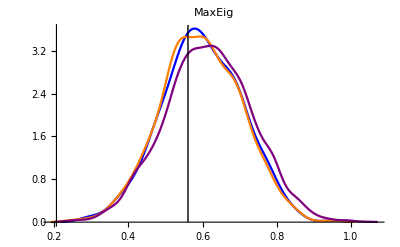

```mathematica
ThreeHistsWithC[MaxEig,4,2,GenDataWithC]
```

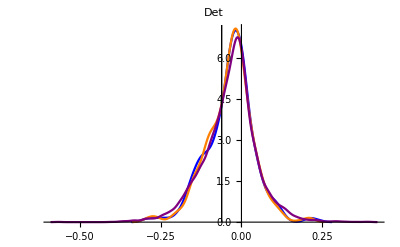

```mathematica
ThreeHistsWithC[Det,4,2,GenDataWithC]
```

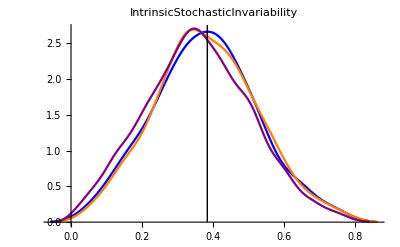

```mathematica
ThreeHistsWithC[IntrinsicStochasticInvariability,4,2,GenDataWithC]
```

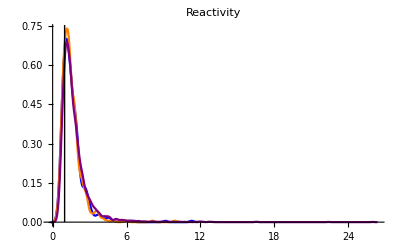

```mathematica
ThreeHistsWithC[Reactivity,4,2,GenDataWithC]
```

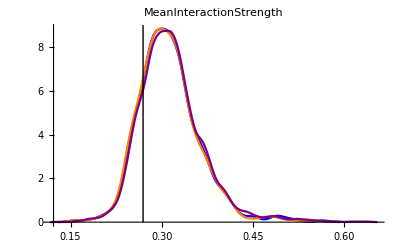

```mathematica
ThreeHistsWithC[MeanInteractionStrength,4,1,GenDataWithC]
```

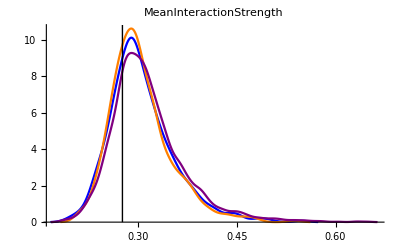

```mathematica
ThreeHistsWithC[MeanInteractionStrength,4,2,GenDataWithC]
```

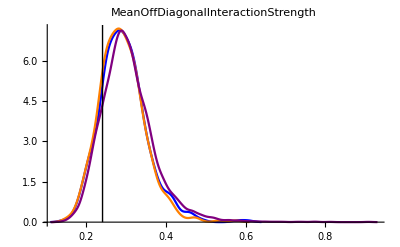

```mathematica
ThreeHistsWithC[MeanOffDiagonalInteractionStrength,4,2,GenDataWithC]
```

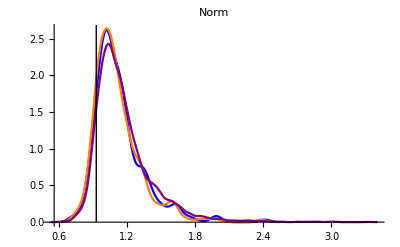

```mathematica
ThreeHistsWithC[Norm,4,2,GenDataWithC]
```

### Things with C (standard deviation = 0.2)

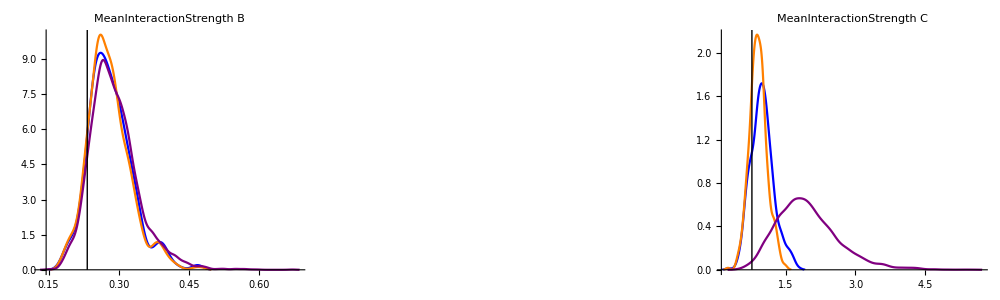

```mathematica
SixHists[MeanInteractionStrength,4,2]
```

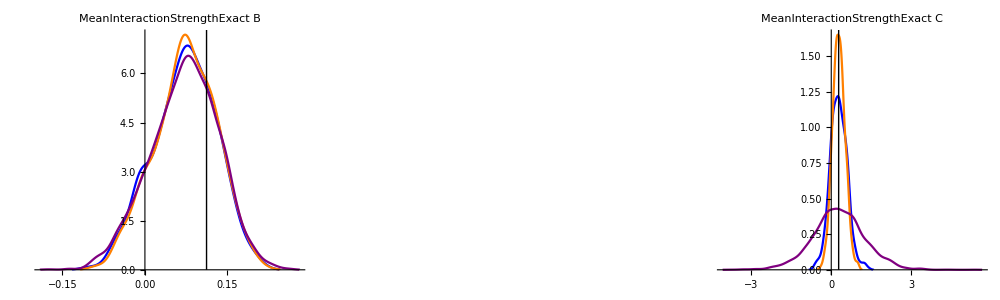

```mathematica
SixHists[MeanInteractionStrengthExact,4,2]
```

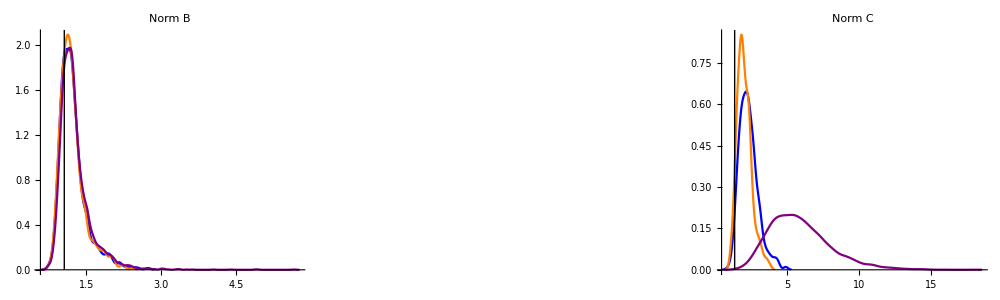

```mathematica
SixHists[Norm,4,2]
```

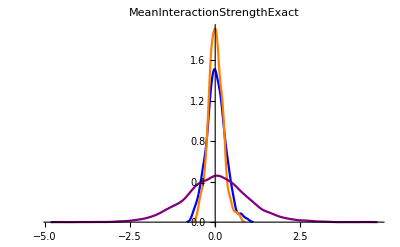

```mathematica
CHistsDifference[MeanInteractionStrengthExact,4,2]
```

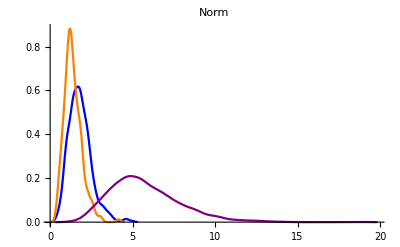

```mathematica
CHistsDifference[Norm,4,2]
```

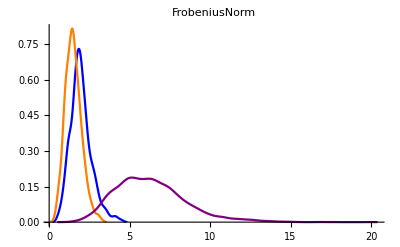

```mathematica
CHistsDifference[FrobeniusNorm,4,2]
```

### Things with C (standard deviation = 10)

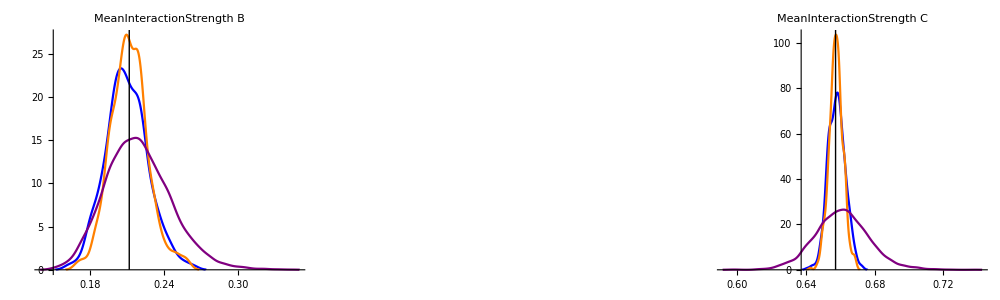

```mathematica
SixHists[MeanInteractionStrength,4,2]
```

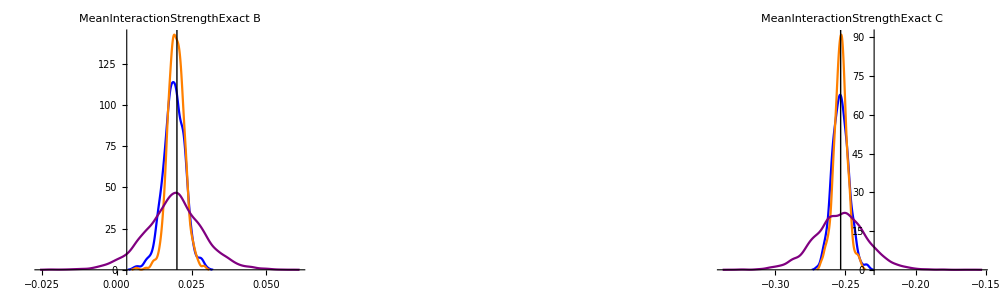

```mathematica
SixHists[MeanInteractionStrengthExact,4,2]
```

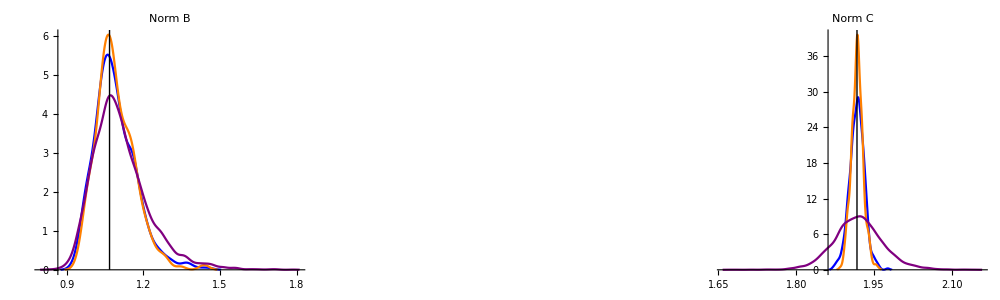

```mathematica
SixHists[Norm,4,2]
```

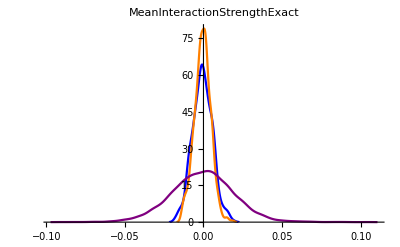

```mathematica
CHistsDifference[MeanInteractionStrengthExact,4,2]
```

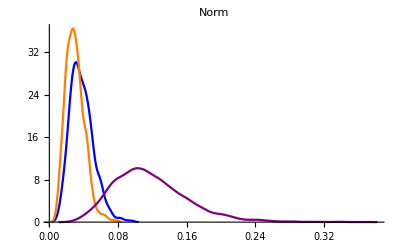

```mathematica
CHistsDifference[Norm,4,2]
```

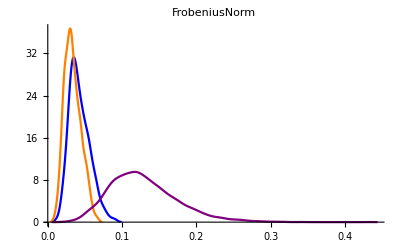

```mathematica
CHistsDifference[FrobeniusNorm,4,2]
```

### Histograms with Covariates and Extra Noise!

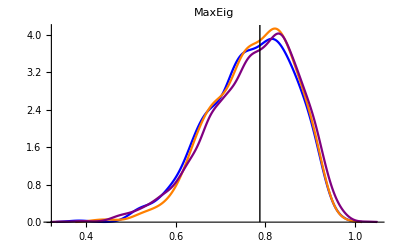

```mathematica
ThreeHistsWithC[MaxEig,4,1,GenDataWithCNoisy]
```

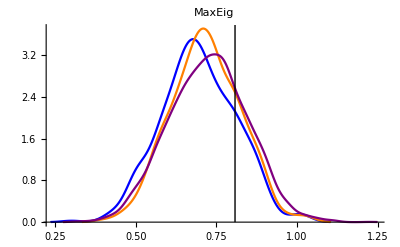

```mathematica
ThreeHistsWithC[MaxEig,4,2,GenDataWithCNoisy]
```

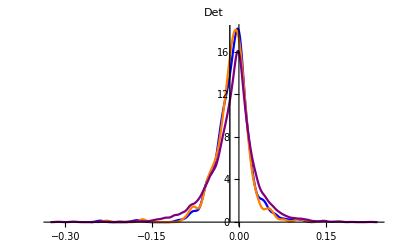

```mathematica
ThreeHistsWithC[Det,4,2,GenDataWithCNoisy]
```

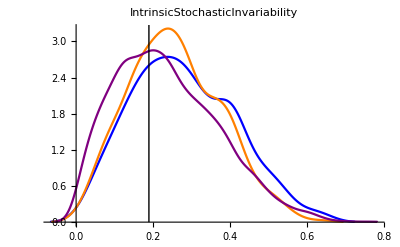

```mathematica
ThreeHistsWithC[IntrinsicStochasticInvariability,4,2,GenDataWithCNoisy]
```

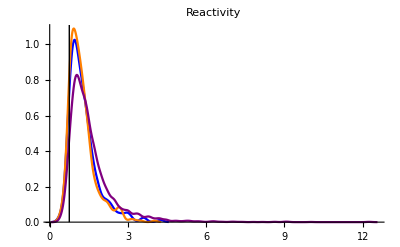

```mathematica
ThreeHistsWithC[Reactivity,4,2,GenDataWithCNoisy]
```

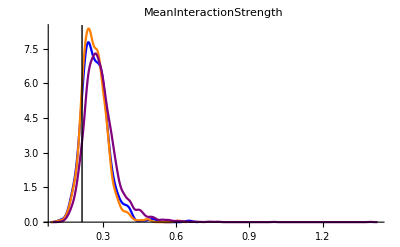

```mathematica
ThreeHistsWithC[MeanInteractionStrength,4,1,GenDataWithCNoisy]
```

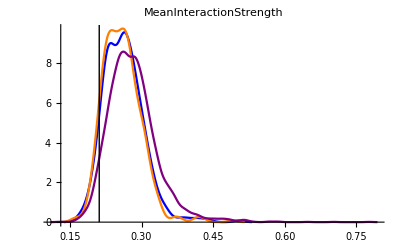

```mathematica
ThreeHistsWithC[MeanInteractionStrength,4,2,GenDataWithCNoisy]
```

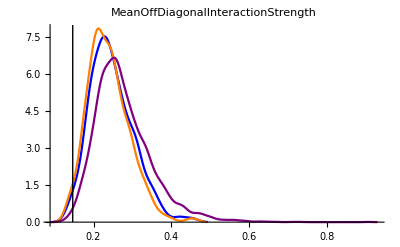

```mathematica
ThreeHistsWithC[MeanOffDiagonalInteractionStrength,4,2,GenDataWithCNoisy]
```

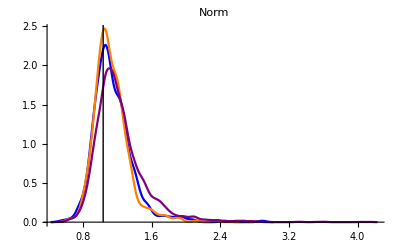

```mathematica
ThreeHistsWithC[Norm,4,2,GenDataWithCNoisy]
```

### A vectors

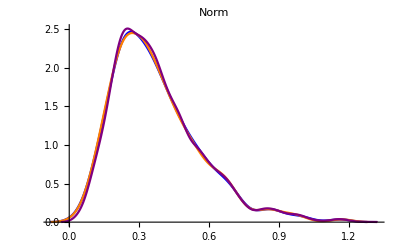

```mathematica
AHists[Norm,4,2]
```

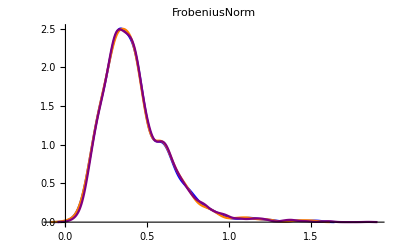

```mathematica
AHists[FrobeniusNorm,4,2]
```

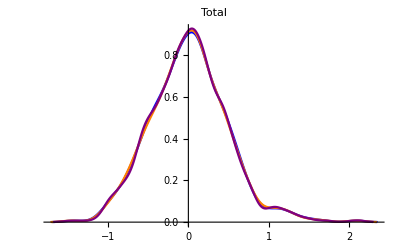

```mathematica
AHists[Total,4,2]
```

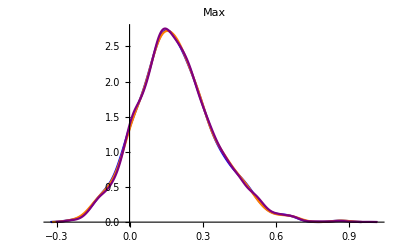

```mathematica
AHists[Max,4,2]
```

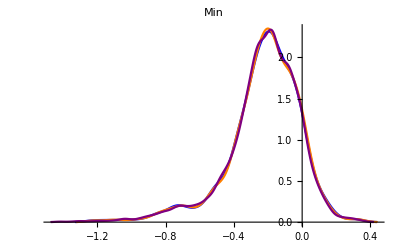

```mathematica
AHists[Min,4,2]
```

### Equilibrium or Not

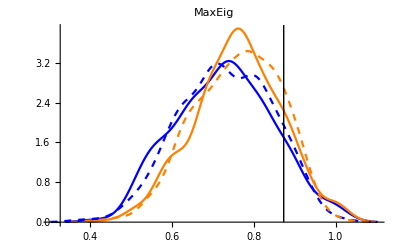

```mathematica
ThreeHistsAllTime[MaxEig,4,1,GenDataWithCNoisy]
```

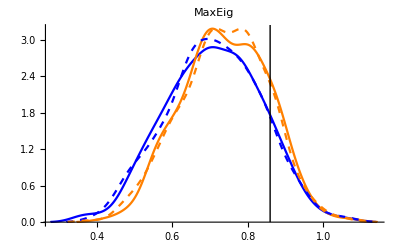

```mathematica
ThreeHistsAllTime[MaxEig,4,2,GenDataWithCNoisy]
```

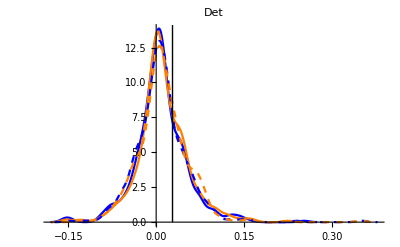

```mathematica
ThreeHistsAllTime[Det,4,2,GenDataWithCNoisy]
```

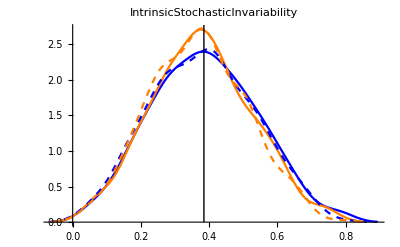

```mathematica
ThreeHistsAllTime[IntrinsicStochasticInvariability,4,2,GenDataWithCNoisy]
```

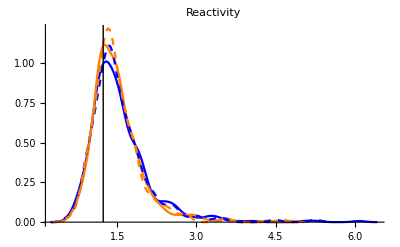

```mathematica
ThreeHistsAllTime[Reactivity,4,2,GenDataWithCNoisy]
```

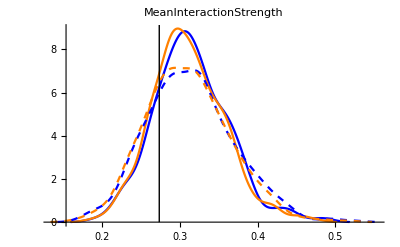

```mathematica
ThreeHistsAllTime[MeanInteractionStrength,4,1,GenDataWithCNoisy]
```

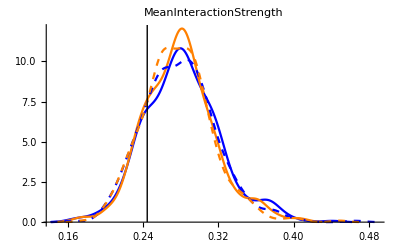

```mathematica
ThreeHistsAllTime[MeanInteractionStrength,4,2,GenDataWithCNoisy]
```

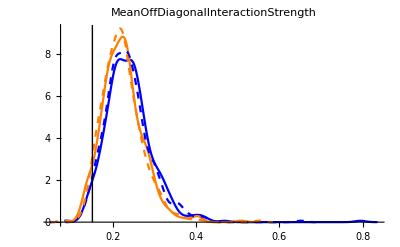

```mathematica
ThreeHistsAllTime[MeanOffDiagonalInteractionStrength,4,2,GenDataWithCNoisy]
```

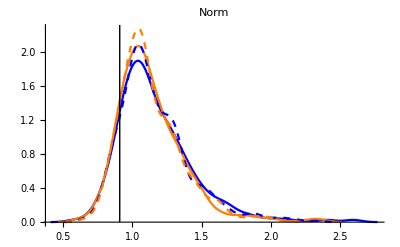

```mathematica
ThreeHistsAllTime[Norm,4,2,GenDataWithCNoisy]
```

### Histograms with Covariates

```mathematica
(* This function creates a histogram of a property (function) of B matrices based on generated data WITH covariates
This uses composite, individual, and averaged matrices 
Specify the function, the number of species, the number of covariates, and if you want to use GenDataWithC or GenDataWithCNoisy (see functions.nb for more information) *)
ThreeHistsWithCNew[function_,size_,covsize_,generator_]:=Module[{listC,listA,listI,useB,useC,useSigma,useData,newBC,newBA,newBI},
listC={};
listA={};
listI={};
useB=GenBNew[size];
useC=GenC[size,covsize];
For[i=1,i≤500,i++,
useSigma=GenSigma[size];
useData=generator[useB,useC,useSigma,10,25,10];  (* the first number is the number of tanks, the second number is the length of time, the third is "fudge time" to let the system settle to an equilibrium *)
newBC=B[MAR[useData,covsize,{}]];
newBA=Table[0,{i,1,size},{j,1,size}];
For[j=1,j≤10,j++,
newBI=B[MAR[{useData[[j]]},covsize,{}]];
newBA=newBI+newBA;
listI=HistList[listI,function,newBI];
];
newBA=newBA/10;
listC=HistList[listC,function,newBC];
listA=HistList[listA,function,newBA];
];
GraphicsRow[{Show[SmoothHistogram[listA,Epilog->Line[{{function[useB],0},{function[useB],150}}],PlotStyle->Blue,PlotRange->All],SmoothHistogram[listC,PlotStyle->Orange,PlotRange->All],SmoothHistogram[listI,PlotStyle->Purple,PlotRange->All],PlotLabel->function,PlotRange->All],LineLegend[{Blue,Orange,Purple},{"Averaged","Composite","Individual"}]},ImageSize->{700,300}]
]
```

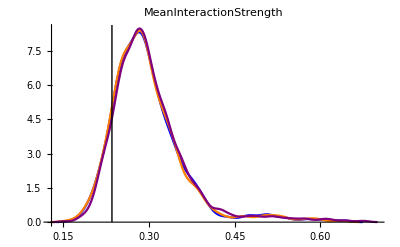

```mathematica
ThreeHistsWithCNew[MeanInteractionStrength,4,1,GenDataWithC]
```

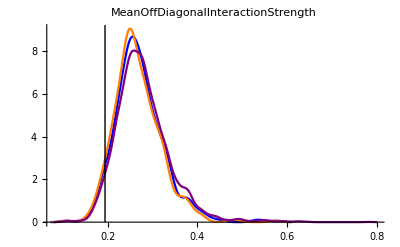

```mathematica
ThreeHistsWithCNew[MeanOffDiagonalInteractionStrength,4,2,GenDataWithC]
```

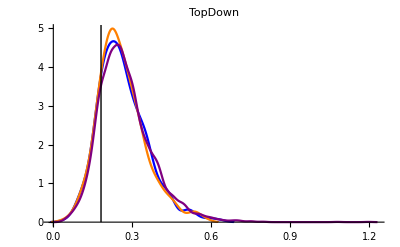

```mathematica
ThreeHistsWithCNew[TopDown,4,2,GenDataWithC]
```

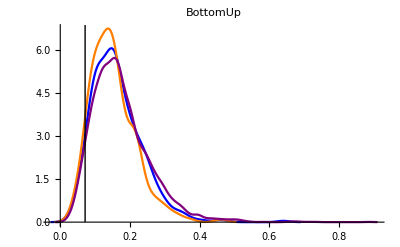

```mathematica
ThreeHistsWithCNew[BottomUp,4,2,GenDataWithC]
```

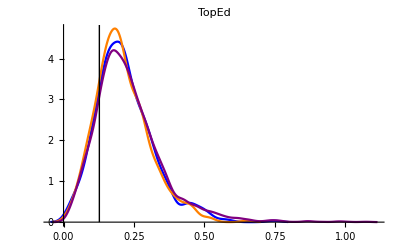

```mathematica
ThreeHistsWithCNew[TopEd,4,2,GenDataWithC]
```

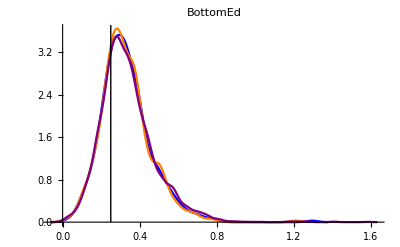

```mathematica
ThreeHistsWithCNew[BottomEd,4,2,GenDataWithC]
```

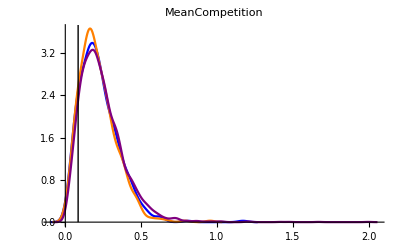

```mathematica
ThreeHistsWithCNew[MeanCompetition,4,2,GenDataWithC]
```